```mathematica
dihedrals={{0.342077002999,-1.31828664974,-1.57079632679},{0.337629650875,-1.30302190575,-1.57079632679},{0.344738876716,-1.35490835203,1.57079632679},{0.33190574737,-1.33078818012,1.57079632679},{0.337166445573,-1.32711750271,1.57079632679},{0.33423255135,-1.32493804535,1.57079632679},{0.335499502938,-1.32404480173,-1.57079632679},{0.323847595241,-1.35219517927,-1.57079632679},{0.333647239254,-1.33076333874,-1.57079632679},{0.335219292107,-1.33087142795,1.57079632679},{0.337686082178,-1.32347680516,1.57079632679},{0.332646965235,-1.32946367828,1.57079632679},{0.337678198668,-1.29786442998,1.57079632679},{0.334510679515,-1.35656203628,1.57079632679},{0.337808610266,-1.32848384698,1.57079632679},{0.333159517064,-1.32848852323,-1.57079632679},{0.335293527917,-1.32894521722,-1.57079632679},{0.333119769498,-1.33869133926,1.57079632679},{0.335958386281,-1.3134768727,-1.57079632679},{0.333135867392,-1.32945743747,-1.57079632679},{0.335195932189,-1.32536662855,1.57079632679},{0.334089226375,-1.32453576153,1.57079632679},{0.339151800192,-1.33120693881,-1.57079632679},{-0.0290211071619,0.963416084106,-1.57079632679},{0.342335269993,-1.31636307557,-1.57079632679},{0.33627448006,-1.32626075974,1.57079632679},{0.331601651819,-1.32516692785,1.57079632679},{0.335415364845,-1.33265832491,-1.57079632679},{0.330343161679,-1.34332042238,1.57079632679},{0.336210760343,-1.31449942963,1.57079632679},{0.332396749449,-1.32257771641,-1.57079632679},{0.336030155774,-1.32742892642,-1.57079632679},{0.334000924799,-1.33064769227,-1.57079632679},{0.330402621767,-1.31765874907,1.57079632679},{0.345253081014,-1.33405289421,-1.57079632679},{0.335263025315,-1.32756232105,-1.57079632679},{0.335217071448,-1.32577722222,-1.57079632679},{0.334958957782,-1.32746201934,1.57079632679},{0.334910370252,-1.3255368149,-1.57079632679},{0.338506801953,-1.31475744002,1.57079632679},{0.340106782191,-1.32315827328,1.57079632679},{0.338845508353,-1.32244067548,-1.57079632679},{0.336008624265,-1.3204870191,1.57079632679},{0.334863030785,-1.31785622269,1.57079632679},{0.346124678386,-1.2812874361,-1.57079632679},{0.33617767072,-1.36980315598,1.57079632679}};
```

```mathematica
d[n_]:=dihedrals[[All,n]]
```

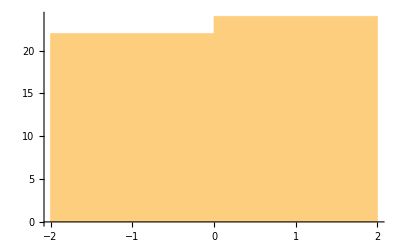

```mathematica
Histogram[d[3],1000]
```

```mathematica
Histogram[d[2]];
```

```mathematica
angles={{-0.0265194112238,0.511116609511},{0.0386195007836,0.413470961861},{-0.0107400644876,0.528220331199},{0.00881364149034,0.489016214103},{-0.00158106268712,0.492805785164},{-0.00293943313559,0.487418151519},{-0.0425698510321,0.452541149034},{0.0427761109414,0.46106443654},{0.000199640842831,0.48302421167},{0.00278367800585,0.491501781039},{-0.0084351549627,0.483087407982},{0.0116103926976,0.517428888688},{-0.0337084261808,0.439249056375},{0.0264202958134,0.500295288193},{-0.00640436215112,0.486542449487},{0.00405972342756,0.480827548107},{0.0028455432619,0.478876119515},{-0.00092815967999,0.51364686845},{-0.00590674879248,0.471404990147},{0.00243413732287,0.486376569498},{-0.0023865579054,0.491629841349},{0.014657768279,0.481324743862},{0.623019790827,-0.295897953267},{-0.561753995941,-0.402340318135},{-0.0227123521203,0.466532778199},{0.00376052535191,0.486113757328},{-0.00113072474661,0.481524186629},{0.00532631257786,0.476523406805},{0.000131922221841,0.51048622915},{-0.00414940283047,0.479695977584},{-0.000775624711215,0.483297424025},{-0.00351521386652,0.482969345457},{-0.0250882433562,0.495174225816},{0.0406558904831,0.441906803014},{-0.0132882367755,0.520105908208},{-0.00154941349949,0.490670900981},{0.00242103542083,0.48466712609},{-0.000223135126515,0.485483723547},{0.0213746881853,0.501768162744},{-0.0131949704437,0.506596372488},{-0.00119833745253,0.498275854454},{0.00695584275204,0.500548945386},{-0.011153879216,0.50067579898},{0.0189707816452,0.541731219658},{-0.0516966481806,0.429678275293}};
```

```mathematica
a[n_]:=angles[[All,n]];
```

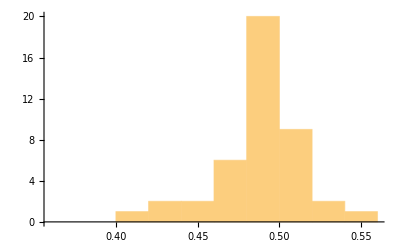

```mathematica
Histogram[a[2]]
```

```mathematica
a[2]
```

{0.511117,0.413471,0.52822,0.489016,0.492806,0.487418,0.452541,0.461064,0.483024,0.491502,0.483087,0.517429,0.439249,0.500295,0.486542,0.480828,0.478876,0.513647,0.471405,0.486377,0.49163,0.481325,-0.295898,-0.40234,0.466533,0.486114,0.481524,0.476523,0.510486,0.479696,0.483297,0.482969,0.495174,0.441907,0.520106,0.490671,0.484667,0.485484,0.501768,0.506596,0.498276,0.500549,0.500676,0.541731,0.429678}